```mathematica
P={-8,11};Q={7,4};
```

```mathematica
V=Q-P
```

{15,-7}

```mathematica
ArrowPlots6=Graphics[{Arrowheads[.07],Thickness[.010],Black,Arrow[{{0,0},P}],Black,Arrow[{{0,0},Q}],Red,Arrow[{P,Q}],Blue,Arrow[{{0,0},V}]}];
```

```mathematica
TxtPlots6=Graphics[{Black,Text["P",{-5,5}],Text["Q",{4.5,1}],Text["PQ",{0,9}],Text["V",{10,-3}]}];
```

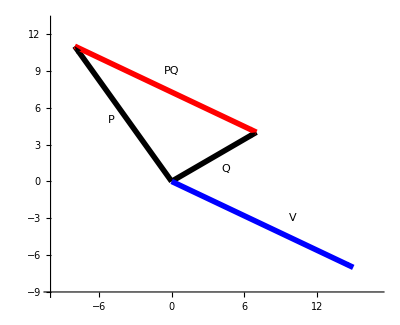

```mathematica
Show[ArrowPlots6,TxtPlots6,PlotRange-> {{-10,17},{-9,13}},Axes-> True,AxesOrigin-> {-10,-9}]
```

```mathematica
A = {{-8, 7},{11, 4}};A//MatrixForm
```

(-8 | 7
11 | 4)